```mathematica
a1[x_]:=Sin[0.1*x]/Sin[0.1];
a2[x_]:=Sin[0.2*x]/Sin[0.2];
a3[x_]:=Sin[0.3*x]/Sin[0.3];
a4[x_]:=Sin[0.4*x]/Sin[0.4];
a5[x_]:=Sin[0.5*x]/Sin[0.5];
a6[x_]:=Sin[0.6*x]/Sin[0.6];
a7[x_]:=Sin[0.7*x]/Sin[0.7];
a8[x_]:=Sin[0.8*x]/Sin[0.8];
a9[x_]:=Sin[0.9*x]/Sin[0.9];
a10[x_]:=Sin[x]/Sin[1];
g1=0.10511370061117786;
g2=0.21782488421166724;
g3=0.3342727525641907;
g4=0.450824199194411;
g5=0.5641895835477562;
g6=0.6715049724420734;
g7=0.7703831838665662;
g8=0.8589370192246678;
g9=0.9357787209128731;
g10=1.0;
M1={a1[0.1],a2[0.1],a3[0.1],a4[0.1],a5[0.1],a6[0.1],a7[0.1],a8[0.1],a9[0.1],a10[0.1]};
M2={a1[0.2],a2[0.2],a3[0.2],a4[0.2],a5[0.2],a6[0.2],a7[0.2],a8[0.2],a9[0.2],a10[0.1]};
M3={a1[0.3],a2[0.3],a3[0.3],a4[0.3],a5[0.3],a6[0.3],a7[0.3],a8[0.3],a9[0.3],a10[0.1]};
M4={a1[0.4],a2[0.4],a3[0.4],a4[0.4],a5[0.4],a6[0.4],a7[0.4],a8[0.4],a9[0.4],a10[0.1]};
M5={a1[0.5],a2[0.5],a3[0.5],a4[0.5],a5[0.5],a6[0.5],a7[0.5],a8[0.5],a9[0.5],a10[0.1]};
M6={a1[0.6],a2[0.6],a3[0.6],a4[0.6],a5[0.6],a6[0.6],a7[0.6],a8[0.6],a9[0.6],a10[0.1]};
M7={a1[0.7],a2[0.7],a3[0.7],a4[0.7],a5[0.7],a6[0.7],a7[0.7],a8[0.7],a9[0.7],a10[0.1]};
M8={a1[0.8],a2[0.8],a3[0.8],a4[0.8],a5[0.8],a6[0.8],a7[0.8],a8[0.8],a9[0.8],a10[0.1]};
M9={a1[0.9],a2[0.9],a3[0.9],a4[0.9],a5[0.9],a6[0.9],a7[0.9],a8[0.9],a9[0.9],a10[0.9]};
M10={a1[1],a2[1],a3[1],a4[1],a5[1],a6[1],a7[1],a8[1],a9[1],a10[1]};
Ma={M1,M2,M3,M4,M5,M6,M7,M8,M9,M10};
Ga={{g1},{g2},{g3},{g4},{g5},{g6},{g7},{g8},{g9},{g10}};
X=LinearSolve[Ma,Ga]
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{0.100165,0.100663,0.101501,0.10269,0.104248,0.106198,0.10857,0.111402,0.11474,0.118642},{0.20032,0.201286,0.20291,0.205216,0.208235,0.212014,0.216609,0.222091,0.22855,0.118642},«7»,{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}} may contain significant numerical errors.

{{6.6177×10^12},{-2.77132×10^13},{3.96224×10^13},{-1.05493×10^13},{-3.36498×10^13},{4.48334×10^13},{-2.5642×10^13},{7.34227×10^12},{-8.61539×10^11},{-0.0366406}}

```mathematica
N[X]
```

{{6.6177×10^12},{-2.77132×10^13},{3.96224×10^13},{-1.05493×10^13},{-3.36498×10^13},{4.48334×10^13},{-2.5642×10^13},{7.34227×10^12},{-8.61539×10^11},{-0.0366406}}

```mathematica
MatrixForm[X]
```

(6.6177×10^12
-2.77132×10^13
3.96224×10^13
-1.05493×10^13
-3.36498×10^13
4.48334×10^13
-2.5642×10^13
7.34227×10^12
-8.61539×10^11
-0.0366406)

```mathematica
f[x_]:=6.6177*10^12*a1[x]-2.77132*10^13*a2[x]+3.96244*10^13*a3[x]-1.05493*10^13*a4[x]-3.36498*10^13*a5[x]+4.48334*10^13*a6[x]-2.5642*10^13*a7[x]+7.34227*10^12*a8[x]-8.61539*10^11*a9[x]-0.0366406*a10[x];
f[0.1]
```

1.95705×10^8

```mathematica
Part[X,1,1]
```

6.6177×10^12

```mathematica
NumberForm[6.617703335740172*^12,16]
```

6.617703335740171×10^12

```mathematica
NumberForm[Part[X,2,1],20]
NumberForm[Part[X,3,1],20]
NumberForm[Part[X,4,1],20]
NumberForm[Part[X,5,1],20]
NumberForm[Part[X,6,1],20]
NumberForm[Part[X,7,1],20]
NumberForm[Part[X,8,1],20]
NumberForm[Part[X,9,1],20]
NumberForm[Part[X,10,1],20]
```

-2.77132145301574×10^13

3.962243416540127×10^13

-1.054928489449636×10^13

-3.364981577515149×10^13

4.483340969148211×10^13

-2.564196403297839×10^13

7.342270972984537×10^12

-8.61538932823401×10^11

-0.03664057375873128

```mathematica
k1="6.617703335740171"×10^("12");
k2="-2.77132145301574"×10^("13");
k3="3.962243416540127"×10^("13");
k4="-1.054928489449636"×10^("13");
k5="-3.364981577515149"×10^("13");
k6="4.483340969148211"×10^("13");
k7="-2.564196403297839"×10^("13");
k8="7.342270972984537"×10^("12");
k9="-8.61538932823401"×10^("11");
k10="-0.03664057375873128";
f[x_]:=k1*a1[x]+k2*a2[x]+k3*a3[x]+k4*a4[x]+k5*a5[x]+k6*a6[x]+k7*a7[x]+k8*a8[x]+k9*a9[x]+k10*a10[x];
f[0.1]
```

0.10498

```mathematica
NumberForm[0.10498046875,16]
```

0.10498046875

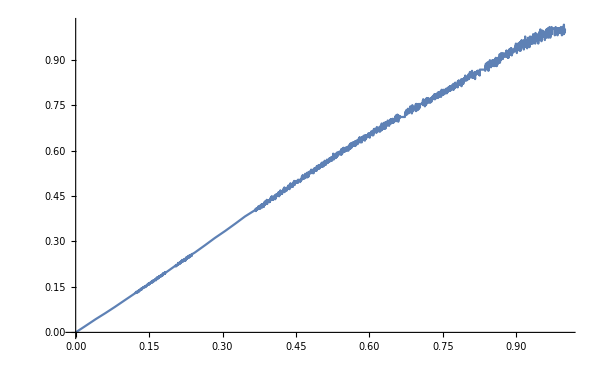

```mathematica
Plot[f[x],{x,0,1},PlotRange->Full]
```

```mathematica
gs1=0.05136084326358388;
gs2=0.10511370061117786;
gs3=0.16076465136631898;
gs4=0.21782488421166724;
gs5=0.27581566283020936;
gs6=0.3342727525641907;
gs7=0.3927503042636112;
gs8=0.450824199194411;
gs9=0.5080948656271651;
gs10=0.5641895835477562;
gs11=0.6187642988516094;
gs12=0.6715049724420734;
gs13=0.7221284928987683;
gs14=0.7703831838665662;
gs15=0.8160489390982628;
gs16=0.8589370192246678;
gs17=0.8988895448871846;
gs18=0.9357787209128731;
gs19=0.9695058258025873;
gs20=1.0;
d1[x_]:=Sin[0.05*x]/Sin[0.05];
d2[x_]:=Sin[0.1*x]/Sin[0.1];
d3[x_]:=Sin[0.15*x]/Sin[0.15];
d4[x_]:=Sin[0.2*x]/Sin[0.2];
d5[x_]:=Sin[0.25*x]/Sin[0.25];
d6[x_]:=Sin[0.3*x]/Sin[0.3];
d7[x_]:=Sin[0.35*x]/Sin[0.35];
d8[x_]:=Sin[0.4*x]/Sin[0.4];
d9[x_]:=Sin[0.45*x]/Sin[0.45];
d10[x_]:=Sin[0.5x]/Sin[0.5];
d11[x_]:=Sin[0.55x]/Sin[0.55];
d12[x_]:=Sin[0.6x]/Sin[0.6];
d13[x_]:=Sin[0.65x]/Sin[0.65];
d14[x_]:=Sin[0.7x]/Sin[0.7];
d15[x_]:=Sin[0.75x]/Sin[0.75];
d16[x_]:=Sin[0.8x]/Sin[0.8];
d17[x_]:=Sin[0.85x]/Sin[0.85];
d18[x_]:=Sin[0.9x]/Sin[0.9];
d19[x_]:=Sin[0.95x]/Sin[0.95];
d20[x_]:=Sin[x]/Sin[1];
Na[x_]:={d1[x],d2[x],d3[x],d4[x],d5[x],d6[x],d7[x],d8[x],d9[x],d10[x],d11[x],d12[x],d13[x],d14[x],d15[x],d16[x],d17[x],d18[x],d19[x],d20[x]};
Nax={Na[0.05],Na[0.1],Na[0.15],Na[0.2],Na[0.25],Na[0.3],Na[0.35],Na[0.4],Na[0.45],Na[0.5],Na[0.55],Na[0.6],Na[0.65],Na[0.7],Na[0.75],Na[0.8],Na[0.85],Na[0.9],Na[0.95],Na[1]};
Gax={{gs1},{gs2},{gs3},{gs4},{gs5},{gs6},{gs7},{gs8},{gs9},{gs10},{gs11},{gs12},{gs13},{gs14},{gs15},{gs16},{gs17},{gs18},{gs19},{gs20}};
X=LinearSolve[Nax,Gax]
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{0.0500208,0.0500832,0.0501875,0.0503341,0.0505233,0.050756,0.051033,0.0513552,0.0517239,0.0521403,«10»},{0.100041,0.100165,0.100372,0.100663,0.101039,0.101501,0.10205,0.10269,0.103422,0.104248,«10»},«8»,«10»} may contain significant numerical errors.

{{1.39321×10^14},{-1.97891×10^14},{9.43313×10^12},{3.69064×10^13},{7.76065×10^13},{-1.28421×10^14},{4.35876×10^13},{3.68088×10^13},{8.91842×10^13},{-1.50969×10^14},{-6.30974×10^12},{9.0609×10^13},{-1.01659×10^14},{9.20787×10^13},{-2.0087×10^13},{6.4098×10^12},{-2.76257×10^13},{-3.66774×10^11},{1.74926×10^13},{-6.1089×10^12}}

```mathematica
NumberForm[Part[X,1,1],20]
NumberForm[Part[X,2,1],20]
NumberForm[Part[X,3,1],20]
NumberForm[Part[X,4,1],20]
NumberForm[Part[X,5,1],20]
NumberForm[Part[X,6,1],20]
NumberForm[Part[X,7,1],20]
NumberForm[Part[X,8,1],20]
NumberForm[Part[X,9,1],20]
NumberForm[Part[X,10,1],20]
NumberForm[Part[X,11,1],20]
NumberForm[Part[X,12,1],20]
NumberForm[Part[X,13,1],20]
NumberForm[Part[X,14,1],20]
NumberForm[Part[X,15,1],20]
NumberForm[Part[X,16,1],20]
NumberForm[Part[X,17,1],20]
NumberForm[Part[X,18,1],20]
NumberForm[Part[X,19,1],20]
NumberForm[Part[X,20,1],20]
fs[x_]:=F1*d1[x]+F2*d2[x]+F3*d3[x]+F4*d4[x]+F5*d5[x]+F6*d6[x]+F7*d7[x]+F8*d8[x]+F9*d9[x]+F10*d10[x]+F11*d11[x]+F12*d12[x]+F13*d13[x]+F14*d14[x]+F15*d15[x]+F16*d16[x]+F17*d17[x]+F18*d18[x]+F19*d19[x]+F20*d20[x];
fs[0.1]//Simplify
```

1.393206552984435×10^14

-1.978908238967336×10^14

9.43312820584176×10^12

3.690635835429462×10^13

7.760652422028127×10^13

-1.284208141907472×10^14

4.358760855360536×10^13

3.680883227736943×10^13

8.91842154553264×10^13

-1.509686997458116×10^14

-6.309742917967842×10^12

9.0609046739429×10^13

-1.016590691051133×10^14

9.20787148580804×10^13

-2.008698797476833×10^13

6.409797339178127×10^12

-2.762565265016325×10^13

-3.667737760028567×10^11

1.749257851901115×10^13

-6.108895563552121×10^12

0.100165 (-1.978908238967336×10^14)+0.104248 (-1.509686997458116×10^14)+0.101501 (-1.284208141907472×10^14)+0.107329 (-1.016590691051133×10^14)+0.113004 (-2.762565265016325×10^13)+0.109926 (-2.008698797476833×10^13)+0.105172 (-6.309742917967842×10^12)+0.118642 (-6.108895563552121×10^12)+0.11474 (-3.667737760028567×10^11)+0.111402 (6.409797339178127×10^12)+0.100372 (9.43312820584176×10^12)+0.116616 (1.749257851901115×10^13)+0.10269 (3.680883227736943×10^13)+0.100663 (3.690635835429462×10^13)+0.10205 (4.358760855360536×10^13)+0.101039 (7.760652422028127×10^13)+0.103422 (8.91842154553264×10^13)+0.106198 (9.0609046739429×10^13)+0.10857 (9.20787148580804×10^13)+0.100041 (1.393206552984435×10^14)

```mathematica
Fs1=N[Part[X,1,1]];
Fs2=N[Part[X,2,1]];
Fs3=N[Part[X,3,1]];
Fs4=N[Part[X,4,1]];
Fs5=N[Part[X,5,1]];
Fs6=N[Part[X,6,1]];
Fs7=N[Part[X,7,1]];
Fs8=N[Part[X,8,1]];
Fs9=N[Part[X,9,1]];
Fs10=N[Part[X,10,1]];
Fs11=N[Part[X,11,1]];
Fs12=N[Part[X,12,1]];
Fs13=N[Part[X,13,1]];
Fs14=N[Part[X,14,1]];
Fs15=N[Part[X,15,1]];
Fs16=N[Part[X,16,1]];
Fs17=N[Part[X,17,1]];
Fs18=N[Part[X,18,1]];
Fs19=N[Part[X,19,1]];
Fs20=N[Part[X,20,1]];
```

1.39321×10^14

```mathematica
fs[x_]:=Fs1*d1[x]+Fs2*d2[x]+Fs3*d3[x]+Fs4*d4[x]+Fs5*d5[x]+Fs6*d6[x]+Fs7*d7[x]+Fs8*d8[x]+Fs9*d9[x]+Fs10*d10[x]+Fs11*d11[x]+Fs12*d12[x]+Fs13*d13[x]+Fs14*d14[x]+Fs15*d15[x]+Fs16*d16[x]+Fs17*d17[x]+Fs18*d18[x]+Fs19*d19[x]+Fs20*d20[x];
fs[0.1]
```

0.105469

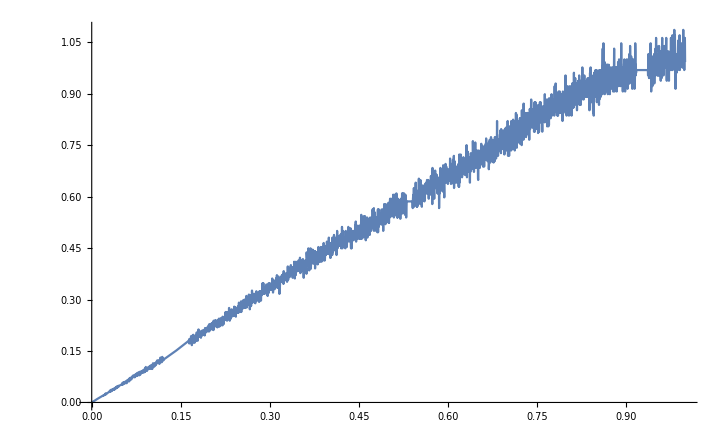

```mathematica
Plot[fs[x],{x,0,1},PlotRange->Full]
```

```mathematica
a1[0.1]
```

0.100165

```mathematica
a1[0.2]
```

0.20032

```mathematica
a10[0.1]
```

0.118642